```mathematica
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
arraynameWithIndex=datastock
];
```

```mathematica
R=8.314;
F=83500;
```

```mathematica
CVSimulationAlpha[length_,dimension_,density_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,mesh,i={},itemp,scanvolt,tempscanrate,counter=0},
mesh=Tuples[Range[length],dimension];
(distribution[#]=density)&/@mesh;
range=Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&];
Analyzer[position_]:=d*Total[Cases[distribution/@((position+#)&/@range)-distribution[position],_Real]];
scanvolt=init;
tempscanrate=scanrate;
While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
itemp=-(standardVolt-scanvolt-8.314*T/n/F*Log[distribution[electrodeposition]])/r;
If[itemp<0,AppendTo[i,{scanvolt,0}],
AppendTo[i,{scanvolt,itemp}];
distribution[electrodeposition]-=itemp;
If[distribution[electrodeposition]<0,distribution[electrodeposition]=0.];
];
distribution[#]+=Analyzer[#]&/@mesh;
];
i
];
```

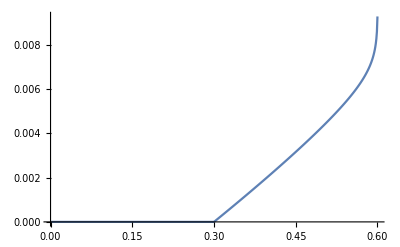

```mathematica
ListLinePlot@%
```

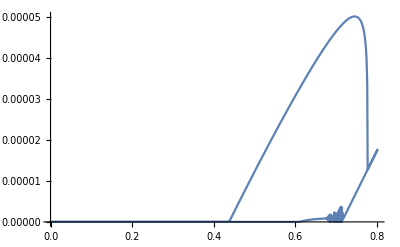

```mathematica
CVSimulationAlpha[100,1,0.01,0.3,1,300,5000,0.0001,{100},0.,0.,0.8,0.001,2];
ListLinePlot[%,PlotRange->All]
```

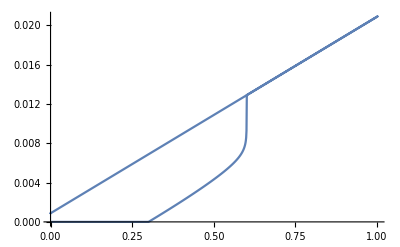

```mathematica
ListLinePlot@%
```

```mathematica
Analyzer[range_,d_,distribution_,position_]:=d*Total[Cases[distribution/@((position+#)&/@range)-distribution[position],_Real]];
```

```mathematica
Clear[A];
```

```mathematica
Table[A[{i,j}]=1,{i,1,10},{j,1,10}];
```

```mathematica
A[{1,2}]
```

1

```mathematica
Table[A[{i,j}]=1.,{i,1,10},{j,1,10}];
A[{5,5}]=0.;
```

```mathematica
A[{5,5}]
```

0

```mathematica
Select[Tuples[{-1,0,1},2],Total[#^2]==1&]+{{1,1}}
```

Thread::tdlen: Objects of unequal length in {{-1,0},{0,-1},{0,1},{1,0}}+{{1,1}} cannot be combined.

{{1,1}}+{{-1,0},{0,-1},{0,1},{1,0}}

```mathematica
(A[#]+=Analyzer[Select[Tuples[{-1,0,1},2],Total[#^2]==1&],0.1,A,#])&/@Flatten[Table[{i,j},{i,10},{j,10}],1]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.4,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,-0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Select[Tuples[{-1,0,1},2],Total[#^2]==1&]
```

{{-1,0},{0,-1},{0,1},{1,0}}

```mathematica
Flatten[Table[{i,j},{i,1,10},{j,1,10}],1]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}}

```mathematica
CVSimulationBeta[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,reduced},
mesh=Tuples[Range[length],dimension];
(distribution[#]=density)&/@mesh;
(reduced[#]=reduceddensity)&/@mesh;
range=Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&];
Analyzer[name_,position_]:=d*Total[Cases[name/@((position+#)&/@range)-name[position],_Real]];
scanvolt=init;
tempscanrate=scanrate;
While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
itemp=-(standardVolt-scanvolt-8.314*T/n/F*Log[distribution[electrodeposition]]+8.314*T/n/F*Log[reduced[electrodeposition]])/r;
If[itemp<0,AppendTo[i,{scanvolt,0}],
AppendTo[i,{scanvolt,itemp}];
distribution[electrodeposition]-=itemp;
If[distribution[electrodeposition]<0,distribution[electrodeposition]=0.];
];
distribution[#]+=Analyzer[#]&/@mesh;
];
i
];
```

```mathematica
DSolve[D[c1[x,t],t]==-D1 D[c1[x,t],x,x]&&D[c2[x,t],t]==D2 D[c2[x,t],x,x]&&c1[0,t]/c2[0,t]==Exp[n F/R/T (a+w t)],{c1,c2},x,t]
```

DSolve[c1^(0,1)[x,t]==-D1 c1^(2,0)[x,t]&&c2^(0,1)[x,t]==D2 c2^(2,0)[x,t]&&c1[0,t]/c2[0,t]==ⅇ^((10043.3 n (a+t w))/T),{c1,c2},x,t]

```mathematica
CVSimulationGamma[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,reduced,Balancer},
mesh=Tuples[Range[length],dimension];
(distribution[#]=density)&/@mesh;
(reduced[#]=reduceddensity)&/@mesh;
range=Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&];
Analyzer[name_,position_]:=d*Total[Cases[name/@((position+#)&/@range)-name[position],_Real]];
Balancer[oxidant_,reductant_,volt_,position_]:=Module[{current},
current=(oxidant[position]-(1+Exp[-standardVolt+volt])^-1(reductant[position]+oxidant[position]))*n F;
oxidant[position]=(1+Exp[-standardVolt+volt])^-1(reductant[position]+oxidant[position]) ;
oxidant[position]=(1-(1+Exp[-standardVolt+volt])^-1)(reductant[position]+oxidant[position]) ;
current
];
scanvolt=init;
tempscanrate=scanrate;
While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
AppendTo[i,{scanvolt,Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]}];
];
i
];
```

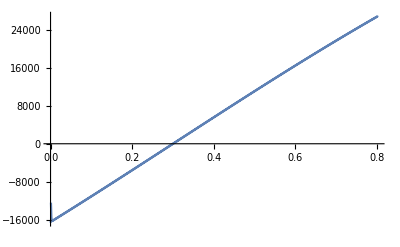

```mathematica
CVSimulationGamma[100,1,1,1,0.3,1,300,5000,0.0001,{{100}},0.,0.,0.8,0.001,2];
ListLinePlot[%,PlotRange->All]
```

```mathematica
First[c1/.NDSolve[D[c1[x,t],t]==D[c1[x,t],x,x]&&D[c2[x,t],t]== D[c2[x,t],x,x]&&1/(c1[0,t]/c2[0,t])==Exp[-0.5+ F/R/300 *0.005 t]&&c1[x,0]==0.001&&c2[x,0]==Exp[-0.5]*0.001&&c1[0,t]+c2[0,t]==0.001*(Exp[-0.5]+1),{c1,c2},{x,0,10},{t,0,10}]][x,t];
Plot[Evaluate[-(D[%,t]-D[%,x,x])*F/.x->0],{t,0,10},PlotRange->All]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {NDSolve[c1^(0,1)[x,t]==c1^(2,0)[x,t]&&c2^(0,1)[x,t]==c2^(2,0)[x,t]&&c2[0,t]/c1[0,t]==ⅇ^(-0.5+0.0000166667 F Power[«2»] t)&&c1[x,0]==0.001&&c2[x,0]==0.000606531&&c1[0,t]+c2[0,t]==0.00160653,{c1,c2},{x,0,10},{t,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

```mathematica
NDSolve[D[c1[x,t],t]==D[c1[x,t],x,x]&&D[c2[x,t],t]== D[c2[x,t],x,x]&&1/(c1[0,t]/c2[0,t])==Exp[-0.5+ F/R/300 *0.005 t]&&c1[x,0]==0.001&&c2[x,0]==Exp[-0.5]*0.001&&c1[0,t]+c2[0,t]==0.001*(Exp[-0.5]+1),{c1,c2},{x,0,10},{t,0,10}]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[c1^(0,1)[x,t]==c1^(2,0)[x,t]&&c2^(0,1)[x,t]==c2^(2,0)[x,t]&&c2[0,t]/c1[0,t]==ⅇ^(-0.5+(0.0000166667 F t)/R)&&c1[x,0]==0.001&&c2[x,0]==0.000606531&&c1[0,t]+c2[0,t]==0.00160653,{c1,c2},{x,0,10},{t,0,10}]

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x$11483. Artificial boundary effects may be present in the solution.

{InterpolatingFunction[…],InterpolatingFunction[…]}

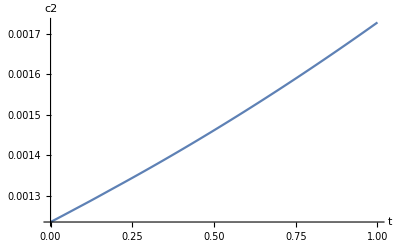

```mathematica
DsolveCV[D1_,D2_,β_,α_,k_,C_,n_,T_,xRange_,tRange_]:=Module[{R,F,c1,c2,x,t,ratio,Solvation},
R=8.314;
F=83500;
ratio=Exp[n*F*β/R/T];
Solvation=NDSolve[{
R*T/n/F*Log[c1[0,t]/c2[0,t]]==β+α*t,
D[c1[x,t],x,x]*D1==D[c1[x,t],t],
D[c2[x,t],x,x]*D2==D[c2[x,t],t],
c2[x,0]==(1+k*ratio)^-1*C,
c1[x,0]==(k+ratio^-1)^-1*C
},
{c1,c2},Flatten[{x,xRange}],Flatten[{t,tRange}]
];
Flatten[{c1,c2}/.Solvation]
];
DsolveCV[1,1,-0.2,0.01,1,1,1,300,{0,100},{0,10}]
Plot[First[%][0,t],{t,0,1},PlotRange->All,AxesLabel->{"t",c2}]
```

```mathematica
DsolveCV[1,1,0.2,0.01,1,1,1,300,{0,10},{0,100}]
```

ReplaceAll::reps: {DSolve[{0.0298707 Log[c1$8245[«2»] Power[«2»]]==0.2+0.01 t$8245,c1$8245^(2,0)[x$8245,t$8245]==c1$8245^(0,1)[x$8245,t$8245],c2$8245^(2,0)[x$8245,t$8245]==c2$8245^(0,1)[x$8245,t$8245],c2$8245[x$8245,0]==0.0012349,c1$8245[x$8245,0]==0.0012349},{c1$8245[x$8245,t$8245],c2$8245[x$8245,t$8245]},{x$8245,0,10},{t$8245,0,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{c1$8245,c2$8245}/.DSolve[{0.0298707 Log[c1$8245[x$8245,t$8245]/c2$8245[x$8245,t$8245]]==0.2+0.01 t$8245,c1$8245^(2,0)[x$8245,t$8245]==c1$8245^(0,1)[x$8245,t$8245],c2$8245^(2,0)[x$8245,t$8245]==c2$8245^(0,1)[x$8245,t$8245],c2$8245[x$8245,0]==0.0012349,c1$8245[x$8245,0]==0.0012349},{c1$8245[x$8245,t$8245],c2$8245[x$8245,t$8245]},{x$8245,0,10},{t$8245,0,100}]

```mathematica
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
datastock
];
```

```mathematica
CVSimulation201[length_,dimension_,density_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,inner,boundary,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,InnerMetaAnalyzer,BoundaryMetaAnalyzer,AnalyzerManipulate,DelayedAnalyzer},
mesh=Tuples[Range[length],dimension];
inner=Tuples[1+Range[length-2],dimension];
boundary=Complement[mesh,inner];


(distribution[#]={density,d})&/@mesh;
range=Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&],dimension],2]];

InnerMetaAnalyzer[name_,position_,rangesingledirection_]:=Total[Times@@@(name/@((position+#)&/@rangesingledirection))]-2*Times@@name[position];
BoundaryMetaAnalyzer[name_,position_,rangesingledirection_]:=Total@Cases[Times@@@(name/@((position+#)&/@Sort[Join@@NestList[rangesingledirection+#&,rangesingledirection,2]]))*{-1.,4.,-5.,-5.,4.,-1.},_Real]+2*Times@@name[position];

Analyzer[name_,position_]:=If[MemberQ[inner,position],
Total[(InnerMetaAnalyzer[name,position,#]&/@range)],
Total[(BoundaryMetaAnalyzer[name,position,#]&/@range)]
];

AnalyzerManipulate[name_,position_,key_]:=Module[{},
ArrayManipulate[Analyzer[name,position]+#&,name[position],key]
];

scanvolt=init;
tempscanrate=scanrate;

DelayedAnalyzer[name_,MESH_]:=Module[{tempstorage},
(tempstorage[#]=AnalyzerManipulate[name,#,1])&/@MESH;
(name[#]=tempstorage[#])&/@MESH;
];


While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
itemp=-(standardVolt-scanvolt-8.314*T/n/F*Log[distribution[electrodeposition][[1]]])/r;
If[itemp<0,AppendTo[i,{scanvolt,0}],
AppendTo[i,{scanvolt,itemp}];
distribution[electrodeposition]=ArrayManipulate[#-itemp&,distribution[electrodeposition],1];
If[distribution[electrodeposition][[1]]<0,Echo[distribution[electrodeposition]];distribution[electrodeposition]=ArrayManipulate[#*0.0001&,distribution[electrodeposition],1]];
];
DelayedAnalyzer[distribution,mesh];
];
i
]
```

Less::nord: Invalid comparison with 0.0000109397+0.0000187683 ⅈ attempted.

Less::nord: Invalid comparison with 0.0000175792+0.0000187683 ⅈ attempted.

Less::nord: Invalid comparison with 0.0000208006+0.0000187683 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

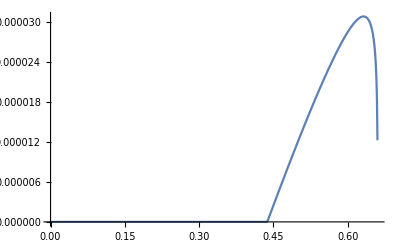

```mathematica
CVSimulation201[100,1,0.01,0.3,1,300,5000,0.01,{100},0.,0.,0.8,0.001,2]; 
%//ListLinePlot
```

```mathematica
Transpose[MapAt[Reverse,Partition[Sort@Select[Tuples[{-1,0,1},7],Total[#^2]==1&],7],2]]
```

{{{-1,0,0,0,0,0,0},{1,0,0,0,0,0,0}},{{0,-1,0,0,0,0,0},{0,1,0,0,0,0,0}},{{0,0,-1,0,0,0,0},{0,0,1,0,0,0,0}},{{0,0,0,-1,0,0,0},{0,0,0,1,0,0,0}},{{0,0,0,0,-1,0,0},{0,0,0,0,1,0,0}},{{0,0,0,0,0,-1,0},{0,0,0,0,0,1,0}},{{0,0,0,0,0,0,-1},{0,0,0,0,0,0,1}}}

```mathematica
Sort[Join@@NestList[{{-1,0,0,0,0,0,0},{1,0,0,0,0,0,0}}+#&,{{-1,0,0,0,0,0,0},{1,0,0,0,0,0,0}},2]]
```

{{-3,0,0,0,0,0,0},{-2,0,0,0,0,0,0},{-1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{2,0,0,0,0,0,0},{3,0,0,0,0,0,0}}

```mathematica
Total[{-1,4,-5,-5,4,-1}*{1,1,1,0,0,0}]
```

-2

```mathematica
A[1]={1,1};
```

```mathematica
First[A[1]]=2
```

Set::write: Tag First in First[{1,1}] is Protected.

2

```mathematica
A[1]
```

{1,1}

```mathematica
Clear[A];
```

```mathematica
A[1]
```

```mathematica
Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},2],Total[#^2]==1&],2],2]]
```

{{{-1,0},{1,0}},{{0,-1},{0,1}}}

```mathematica
CVSimulation202[length_,dimension_,density_,standardVolt_,n_,T_,r_,d_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,inner,boundary,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,InnerMetaAnalyzer,BoundaryMetaAnalyzer,AnalyzerManipulate,DelayedAnalyzer},
mesh=Tuples[Range[length],dimension];
inner=Tuples[1+Range[length-2],dimension];
boundary=Complement[mesh,inner];


(distribution[#]={density,d})&/@mesh;
range=Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&],dimension],2]];

InnerMetaAnalyzer[name_,position_,rangesingledirection_]:=Total[Times@@@(name/@((position+#)&/@rangesingledirection))]-2*Times@@name[position];
BoundaryMetaAnalyzer[name_,position_,rangesingledirection_]:=Total@Cases[Times@@@(name/@((position+#)&/@Sort[Join@@NestList[rangesingledirection+#&,rangesingledirection,2]]))*{-1.,4.,-5.,-5.,4.,-1.},_Real]+2*Times@@name[position];

Analyzer[name_,position_]:=If[MemberQ[inner,position],
Total[(InnerMetaAnalyzer[name,position,#]&/@range)],
Total[(BoundaryMetaAnalyzer[name,position,#]&/@range)]
];

AnalyzerManipulate[name_,position_,key_]:=Module[{},
ArrayManipulate[Analyzer[name,position]+#&,name[position],key]
];

scanvolt=init;
tempscanrate=scanrate;

DelayedAnalyzer[name_,MESH_]:=Module[{tempstorage},
(tempstorage[#]=AnalyzerManipulate[name,#,1])&/@MESH;
(name[#]=tempstorage[#])&/@MESH;
];


While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
itemp=-(standardVolt-scanvolt-8.314*T/n/F*Log[distribution[electrodeposition][[1]]])/r;
If[itemp<0,AppendTo[i,{scanvolt,0}],
AppendTo[i,{scanvolt,itemp}];
distribution[electrodeposition]=ArrayManipulate[#-itemp&,distribution[electrodeposition],1];
If[distribution[electrodeposition][[1]]<0,Echo[distribution[electrodeposition]];distribution[electrodeposition]=ArrayManipulate[#*0.0001&,distribution[electrodeposition],1]];
];
DelayedAnalyzer[distribution,mesh];
];
i
]
```

```mathematica
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
datastock
];
```

```mathematica
CVSimulation202[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,inner,boundary,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,InnerMetaAnalyzer,BoundaryMetaAnalyzer,AnalyzerManipulate,DelayedAnalyzer,reduced,Balancer},
mesh=Tuples[Range[length],dimension];
inner=Tuples[1+Range[length-2],dimension];
boundary=Complement[mesh,inner];


(distribution[#]={density,d1})&/@mesh;
(reduced[#]={reduceddensity,dreduced})&/@mesh;

range=Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&],dimension],2]];

InnerMetaAnalyzer[name_,position_,rangesingledirection_]:=Total[Times@@@(name/@((position+#)&/@rangesingledirection))]-2*Times@@name[position];
BoundaryMetaAnalyzer[name_,position_,rangesingledirection_]:=Total@Cases[Times@@@(name/@((position+#)&/@Sort[Join@@NestList[rangesingledirection+#&,rangesingledirection,2]]))*{-1.,4.,-5.,-5.,4.,-1.},_Real]+2*Times@@name[position];

Analyzer[name_,position_]:=If[MemberQ[inner,position],
Total[(InnerMetaAnalyzer[name,position,#]&/@range)],
Total[(BoundaryMetaAnalyzer[name,position,#]&/@range)]
];

AnalyzerManipulate[name_,position_,key_]:=Module[{},
ArrayManipulate[Analyzer[name,position]+#&,name[position],key]
];

scanvolt=init;
tempscanrate=scanrate;

DelayedAnalyzer[name_,MESH_]:=Module[{tempstorage},
(tempstorage[#]=AnalyzerManipulate[name,#,1])&/@MESH;
(name[#]=tempstorage[#])&/@MESH;
];


Balancer[oxidant_,reductant_,volt_,position_]:=Module[{current},
current=(oxidant[position][[1]]-(1+Exp[-standardVolt+volt])^-1(reductant[position][[1]]+oxidant[position][[1]]))*n F;
oxidant[position]=AnalyzerManipulate[(1+Exp[-standardVolt+volt])^-1(reductant[position][[1]]+#) &,
oxidant[position],1];
oxidant[position]=AnalyzerManipulate[(1-(1+Exp[-standardVolt+volt])^-1)(reductant[position]+#)&,oxidant[position],1] ;
current
];

While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
AppendTo[i,{scanvolt,Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]}];
DelayedAnalyzer[distribution,mesh];
DelayedAnalyzer[reduced,mesh];
];
i
]
```

```mathematica
CVSimulation202[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,init_,start_,end_,scanrate_,segment_]
```

```mathematica
CVSimulation202[100,1,1,1,0.3,1,300,0.0001,0.0001,{{100}},0.,0.,0.8,0.001,2]
```

Thread::tdlen: Objects of unequal length in {1,0.0001}+{-3} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,0.0001}+{-2} cannot be combined.

Thread::tdlen: Objects of unequal length in {1,0.0001}+{-1} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted

```mathematica
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
datastock
];
```

```mathematica
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
datastock
];
CVSimulation202[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,inner,boundary,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,InnerMetaAnalyzer,BoundaryMetaAnalyzer,AnalyzerManipulate,DelayedAnalyzer,reduced,Balancer},
mesh=Tuples[Range[length],dimension];
inner=Tuples[1+Range[length-2],dimension];
boundary=Complement[mesh,inner];


(distribution[#]={density,d1})&/@mesh;
(reduced[#]={reduceddensity,dreduced})&/@mesh;

range=Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&],dimension],2]];

InnerMetaAnalyzer[name_,position_,rangesingledirection_]:=Total[Times@@@(name/@((position+#)&/@rangesingledirection))]-2*Times@@name[position];
BoundaryMetaAnalyzer[name_,position_,rangesingledirection_]:=Total@Cases[Times@@@(name/@((position+#)&/@Sort[Join@@NestList[rangesingledirection+#&,rangesingledirection,2]]))*{-1.,4.,-5.,-5.,4.,-1.},_Real]+2*Times@@name[position];

Analyzer[name_,position_]:=If[MemberQ[inner,position],
Total[(InnerMetaAnalyzer[name,position,#]&/@range)],
Total[(BoundaryMetaAnalyzer[name,position,#]&/@range)]
];

AnalyzerManipulate[name_,position_,key_]:=Module[{},
ArrayManipulate[Analyzer[name,position]+#&,name[position],key]
];

scanvolt=init;
tempscanrate=scanrate;

DelayedAnalyzer[name_,MESH_]:=Module[{tempstorage},
(tempstorage[#]=AnalyzerManipulate[name,#,1])&/@MESH;
(name[#]=tempstorage[#])&/@MESH;
];


Balancer[oxidant_,reductant_,volt_,position_]:=Module[{current},
current=(oxidant[position][[1]]-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+oxidant[position][[1]]));
oxidant[position]=ArrayManipulate[((1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+#)) &,
oxidant[position],1];
reductant[position]=ArrayManipulate[((1-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1)(reductant[position][[1]]+#))&,oxidant[position],1] ;
current
];

While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
AppendTo[i,{scanvolt,Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]}];
DelayedAnalyzer[distribution,mesh];
DelayedAnalyzer[reduced,mesh];
];
i
]
```

```mathematica
CVSimulation202[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,init_,start_,end_,scanrate_,segment_]
```

Range::range: Range specification in Range[length_] does not have appropriate bounds.

Tuples::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Tuples[Range[length_],dimension_].

Range::range: Range specification in Range[-2+length_] does not have appropriate bounds.

Tuples::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Tuples[1+Range[-2+length_],dimension_].

Range::range: Range specification in Range[length] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Tuples::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Tuples[{density_,d1_},{density_,d1_}].

General::stop: Further output of Tuples::ilsmn will be suppressed during this calculation.

Tuples::argt: Tuples called with 0 arguments; 1 or 2 arguments are expected.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Tuples[],dimension_].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Tuples[],Pattern[_,dimension]].

{}

```mathematica
CVSimulation202[30,2,0.4,0.2,0.5,1,300,0.001,0.001,{{15,15}},0.,0.,1.0,0.01,2]
```

{{0.01,-16700.},{0.02,-66.7997},{0.03,-66.7311},{0.04,-66.6637},{0.05,-66.5963},{0.06,-66.5286},{0.07,-66.4606},{0.08,-66.392},{0.09,-66.3223},{0.1,-66.2511},{0.11,-66.1776},{0.12,-66.101},{0.13,-66.0198},{0.14,-65.932},{0.15,-65.8351},{0.16,-65.7251},{0.17,-65.5969},{0.18,-65.4431},{0.19,-65.2534},{0.2,-65.0135},{0.21,-64.7033},{0.22,-64.2947},{0.23,-63.7485},{0.24,-63.01},{0.25,-62.0027},{0.26,-60.6196},{0.27,-58.7116},{0.28,-56.0702},{0.29,-52.4046},{0.3,-47.3094},{0.31,-40.2194},{0.32,-30.3479},{0.33,-16.6022},{0.34,2.53293},{0.35,29.1506},{0.36,66.1293},{0.37,117.401},{0.38,188.285},{0.39,285.878},{0.4,419.457},{0.41,600.772},{0.42,843.993},{0.43,1164.83},{0.44,1578.05},{0.45,2092.29},{0.46,2701.13},{0.47,3370.64},{0.48,4027.49},{0.49,4557.59},{0.5,4829.53},{0.51,4747.4},{0.52,4309.28},{0.53,3623.59},{0.54,2857.59},{0.55,2155.24},{0.56,1588.9},{0.57,1166.37},{0.58,863.385},{0.59,649.508},{0.6,499.06},{0.61,393.089},{0.62,318.24},{0.63,265.221},{0.64,227.567},{0.65,200.766},{0.66,181.651},{0.67,167.994},{0.68,158.218},{0.69,151.205},{0.7,146.161},{0.71,142.523},{0.72,139.886},{0.73,137.966},{0.74,136.556},{0.75,135.512},{0.76,134.729},{0.77,134.132},{0.78,133.669},{0.79,133.302},{0.8,133.002},{0.81,132.752},{0.82,132.537},{0.83,132.347},{0.84,132.175},{0.85,132.016},{0.86,131.867},{0.87,131.725},{0.88,131.588},{0.89,131.455},{0.9,131.324},{0.91,131.196},{0.92,131.069},{0.93,130.944},{0.94,130.82},{0.95,130.696},{0.96,130.574},{0.97,130.452},{0.98,130.331},{0.99,130.21},{1.,130.09},{1.01,129.971},{1.,129.851},{0.99,129.732},{0.98,129.614},{0.97,129.496},{0.96,129.379},{0.95,129.262},{0.94,129.145},{0.93,129.028},{0.92,128.911},{0.91,128.794},{0.9,128.677},{0.89,128.558},{0.88,128.439},{0.87,128.318},{0.86,128.194},{0.85,128.066},{0.84,127.932},{0.83,127.79},{0.82,127.636},{0.81,127.466},{0.8,127.273},{0.79,127.047},{0.78,126.775},{0.77,126.44},{0.76,126.016},{0.75,125.467},{0.74,124.743},{0.73,123.776},{0.72,122.47},{0.71,120.689},{0.7,118.246},{0.69,114.879},{0.68,110.223},{0.67,103.769},{0.66,94.8107},{0.65,82.3645},{0.64,65.0664},{0.63,41.0298},{0.62,7.65531},{0.61,-38.6179},{0.6,-102.625},{0.59,-190.842},{0.58,-311.766},{0.57,-476.164},{0.56,-696.896},{0.55,-987.704},{0.54,-1359.94},{0.53,-1815.92},{0.52,-2338.32},{0.51,-2878.05},{0.5,-3349.44},{0.49,-3645.92},{0.48,-3681.8},{0.47,-3440.46},{0.46,-2989.44},{0.45,-2444.44},{0.44,-1911.73},{0.43,-1453.54},{0.42,-1088.94},{0.41,-811.619},{0.4,-605.949},{0.39,-455.54},{0.38,-346.413},{0.37,-267.601},{0.36,-210.84},{0.35,-170.028},{0.34,-140.712},{0.33,-119.666},{0.32,-104.558},{0.31,-93.7122},{0.3,-85.9228},{0.29,-80.3243},{0.28,-76.2958},{0.27,-73.3922},{0.26,-71.2945},{0.25,-69.774},{0.24,-68.6671},{0.23,-67.8564},{0.22,-67.2578},{0.21,-66.8113},{0.2,-66.4738},{0.19,-66.2143},{0.18,-66.0108},{0.17,-65.8474},{0.16,-65.7129},{0.15,-65.599},{0.14,-65.5001},{0.13,-65.4119},{0.12,-65.3314},{0.11,-65.2566},{0.1,-65.1858},{0.09,-65.1181},{0.08,-65.0525},{0.07,-64.9886},{0.06,-64.926},{0.05,-64.8643},{0.04,-64.8034},{0.03,-64.743},{0.02,-64.6832},{0.01,-64.6238},{-8.67362×10^-17,-64.5647},{0.01,-64.5045}}

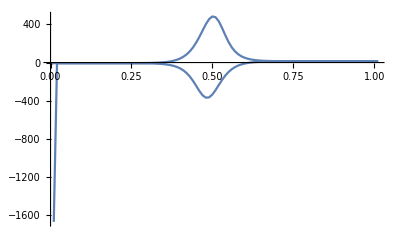

```mathematica
ListLinePlot[%,PlotRange->All]
```

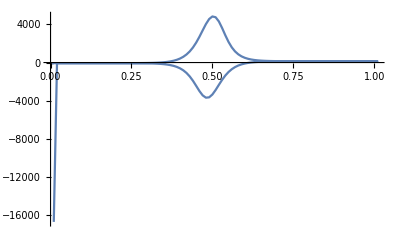

```mathematica
ListLinePlot[%103,PlotRange->All]
```

```mathematica
R=8.314;F=86500;
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
datastock
];
CVSimulation202[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,init_,start_,end_,scanrate_,segment_]:=
Module[{Analyzer,range,distribution,inner,boundary,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,InnerMetaAnalyzer,BoundaryMetaAnalyzer,AnalyzerManipulate,DelayedAnalyzer,reduced,Balancer},
mesh=Tuples[Range[length],dimension];
inner=Tuples[1+Range[length-2],dimension];
boundary=Complement[mesh,inner];


(distribution[#]={density,d1})&/@mesh;
(reduced[#]={reduceddensity,dreduced})&/@mesh;

range=Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&],dimension],2]];

InnerMetaAnalyzer[name_,position_,rangesingledirection_]:=Total[Times@@@(name/@((position+#)&/@rangesingledirection))]-2*Times@@name[position];
BoundaryMetaAnalyzer[name_,position_,rangesingledirection_]:=Total@Cases[Times@@@(name/@((position+#)&/@Sort[Join@@NestList[rangesingledirection+#&,rangesingledirection,2]]))*{-1.,4.,-5.,-5.,4.,-1.},_Real]+2*Times@@name[position];

Analyzer[name_,position_]:=If[MemberQ[inner,position],
Total[(InnerMetaAnalyzer[name,position,#]&/@range)],
Total[(BoundaryMetaAnalyzer[name,position,#]&/@range)]
];

AnalyzerManipulate[name_,position_,key_]:=Module[{},
ArrayManipulate[Analyzer[name,position]+#&,name[position],key]
];

scanvolt=init;
tempscanrate=scanrate;

DelayedAnalyzer[name_,MESH_]:=Module[{tempstorage},
(tempstorage[#]=AnalyzerManipulate[name,#,1])&/@MESH;
(name[#]=tempstorage[#])&/@MESH;
];


Balancer[oxidant_,reductant_,volt_,position_]:=Module[{current},
current=(oxidant[position][[1]]-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+oxidant[position][[1]]));
oxidant[position]=ArrayManipulate[((1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+#)) &,
oxidant[position],1];
reductant[position]=ArrayManipulate[((1-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1)(reductant[position][[1]]+#))&,oxidant[position],1] ;
current
];

While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
AppendTo[i,{scanvolt,Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]}];
DelayedAnalyzer[distribution,mesh];
DelayedAnalyzer[reduced,mesh];
];
i
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
R=8.314;F=86500;
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
datastock
];
CVSimulation203[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,init_,start_,end_,scanrate_,segment_,Logfilename_,ResultFileName_]:=
Module[{Analyzer,range,distribution,inner,boundary,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,InnerMetaAnalyzer,BoundaryMetaAnalyzer,AnalyzerManipulate,DelayedAnalyzer,reduced,Balancer,fileoperator,Resultfileoperator},
mesh=Tuples[Range[length],dimension];
inner=Tuples[1+Range[length-2],dimension];
boundary=Complement[mesh,inner];


fileoperator=OpenWrite[Logfilename];
Resultfileoperator=OpenWrite[ResultFileName];
WriteString[fileoperator,
(StringJoin@Transpose[{(StringInsert[#," = ",-1]&/@{"length","dimension","density","reduceddensity","standardVolt","n","T","d1","dreduced","electrodeposition","init","start","end","scanrate","segment"}),ToString/@{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,init,start,end,scanrate,segment},Table["\n",15]}])<>"\n"
];

WriteString[Resultfileoperator,
(StringJoin@Transpose[{(StringInsert[#," = ",-1]&/@{"length","dimension","density","reduceddensity","standardVolt","n","T","d1","dreduced","electrodeposition","init","start","end","scanrate","segment"}),ToString/@{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,init,start,end,scanrate,segment},Table["\n",15]}])<>"\n"<>"Voltage      "<>"Current"<>"\n"
];


(distribution[#]={density,d1})&/@mesh;
(reduced[#]={reduceddensity,dreduced})&/@mesh;

range=Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&],dimension],2]];

InnerMetaAnalyzer[name_,position_,rangesingledirection_]:=Total[Times@@@(name/@((position+#)&/@rangesingledirection))]-2*Times@@name[position];
BoundaryMetaAnalyzer[name_,position_,rangesingledirection_]:=Total@Cases[Times@@@(name/@((position+#)&/@Sort[Join@@NestList[rangesingledirection+#&,rangesingledirection,2]]))*{-1.,4.,-5.,-5.,4.,-1.},_Real]+2*Times@@name[position];

Analyzer[name_,position_]:=If[MemberQ[inner,position],
Total[(InnerMetaAnalyzer[name,position,#]&/@range)],
Total[(BoundaryMetaAnalyzer[name,position,#]&/@range)]
];

AnalyzerManipulate[name_,position_,key_]:=Module[{},
ArrayManipulate[Analyzer[name,position]+#&,name[position],key]
];

scanvolt=init;
tempscanrate=scanrate;

DelayedAnalyzer[name_,MESH_]:=Module[{tempstorage},
(tempstorage[#]=AnalyzerManipulate[name,#,1])&/@MESH;
(name[#]=tempstorage[#])&/@MESH;
];


Balancer[oxidant_,reductant_,volt_,position_]:=Module[{current},
current=(oxidant[position][[1]]-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+oxidant[position][[1]]));
oxidant[position]=ArrayManipulate[((1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+#)) &,
oxidant[position],1];
reductant[position]=ArrayManipulate[((1-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1)(reductant[position][[1]]+#))&,oxidant[position],1] ;
current
];

WriteString[fileoperator,
"At Scanvolt = "<>ToString[scanvolt]<>" in Segment "<>ToString[segment]<>"\n\n"<>"Oxidized:"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,distribution/@mesh}]]<>"EndFLag"<>"\n\n"<>"Reduced"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,reduced/@mesh}]]<>"EndFLag"<>"\n\n"<>"Reduced"<>"\n\n"
];

While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
WriteString[Resultfileoperator,
ToString[FortranForm@scanvolt]<>"      "<>ToString[FortranForm@Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]]<>"\n"
]
(*AppendTo[i,{scanvolt,Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]}]*)
(*上面的为需要直接在notebook里输出的时候*)
DelayedAnalyzer[distribution,mesh];
DelayedAnalyzer[reduced,mesh];
WriteString[fileoperator,
"At Scanvolt = "<>ToString[scanvolt]<>" in Segment "<>ToString[segment]<>"\n\n"<>"Oxidized:"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,distribution/@mesh}]]<>"EndFLag"<>"\n\n"<>"Reduced"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,reduced/@mesh}]]<>"EndFLag"<>"\n\n"<>"Reduced"<>"\n\n"
];
];

Close[fileoperator];
Close[Resultfileoperator];
]
```

```mathematica
CVSimulation203[30,2,0.4,0.2,0.5,1,300,0.001,0.001,{{15,15}},0.,0.,1.0,0.01,2,"test1.txt","test2.txt"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Apple/Documents/GitHub/Mathematica-Files

```mathematica
stmp=OpenWrite["test.txt"];
Do[WriteString[stmp,ToString["test "]<>"str1"<>ToString["test "]<>"str2"<>"\n"],5];
Close[stmp]
```

test.txt

```mathematica
stmp=OpenWrite["test.txt"];
Do[WriteString[stmp,ToString[Table[i,{i,5}]]<>"\n"],5];
Close[stmp]
```

test.txt

```mathematica
ToExpression/@StringSplit[Import["test.txt"],"\n"]
```

{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
StringJoin@Transpose[{(StringInsert[#," = ",-1]&/@{"length","dimension","density","reduceddensity","standardVolt","n","T","d1","dreduced","electrodeposition","init","start","end","scanrate","segment"}),ToString/@{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,init,start,end,scanrate,segment},Table["\n",15]}]
```

length = length
dimension = dimension
density = density
reduceddensity = reduceddensity
standardVolt = standardVolt
n = n
T = T
d1 = d1
dreduced = dreduced
electrodeposition = electrodeposition
init = init
start = start
end = end
scanrate = scanrate
segment = segment

```mathematica
{"length","dimension","density","reduceddensity","standardVolt","n","T","d1","dreduced","electrodeposition","init","start","end","scanrate","segment"}
```

```mathematica
{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,init,start,end,scanrate,segment}//Length
```

15

```mathematica
ToString/@{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,init,start,end,scanrate,segment}
```

{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,init,start,end,scanrate,segment}

```mathematica
ToString[Range[5]]
```

{1, 2, 3, 4, 5}

```mathematica
ToExpression@(ToString@FortranForm[5.02*10^-15])
```

-15+5.02 e

```mathematica
ToExpression@ToString[5.02*10^15]
```

50.2

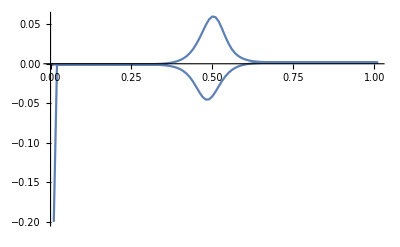

```mathematica
ListLinePlot[Cases[Import["test2.txt","Table"],{_Real,_Real}],PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]];
R=8.314;F=86500;
ArrayManipulate[function_,arraynameWithIndex_,position_]:=Module[{datastock},
datastock=arraynameWithIndex;
datastock[[position]]=function[datastock[[position]]];
datastock
];
```

```mathematica
CVSimulation203[length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,ElectrodePositionOxidizedD_,ElectrodePositionReducedD_,init_,start_,end_,scanrate_,segment_,Logfilename_,ResultFileName_]:=
Module[{Analyzer,range,distribution,inner,boundary,mesh,i={},itemp,scanvolt,tempscanrate,counter=0,InnerMetaAnalyzer,BoundaryMetaAnalyzer,AnalyzerManipulate,DelayedAnalyzer,reduced,Balancer,fileoperator,Resultfileoperator},
mesh=Tuples[Range[length],dimension];
inner=Tuples[1+Range[length-2],dimension];
boundary=Complement[mesh,inner];


fileoperator=OpenWrite[Logfilename];
Resultfileoperator=OpenWrite[ResultFileName];
WriteString[fileoperator,
(StringJoin@Transpose[{(StringInsert[#," = ",-1]&/@{"length","dimension","density","reduceddensity","standardVolt","n","T","d1","dreduced","electrodeposition","ElectrodePositionOxidizedD","ElectrodePositionReducedD","init","start","end","scanrate","segment"}),ToString/@{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,ElectrodePositionOxidizedD,ElectrodePositionReducedD,init,start,end,scanrate,segment},Table["\n",17]}])<>"\n"
];

WriteString[Resultfileoperator,
(StringJoin@Transpose[{(StringInsert[#," = ",-1]&/@{"length","dimension","density","reduceddensity","standardVolt","n","T","d1","dreduced","electrodeposition","ElectrodePositionOxidizedD","ElectrodePositionReducedD","init","start","end","scanrate","segment"}),ToString/@{length,dimension,density,reduceddensity,standardVolt,n,T,d1,dreduced,electrodeposition,ElectrodePositionOxidizedD,ElectrodePositionReducedD,init,start,end,scanrate,segment},Table["\n",17]}])<>"\n"
];


(distribution[#]={density,d1})&/@mesh;
(reduced[#]={reduceddensity,dreduced})&/@mesh;

(distribution[#]={density,ElectrodePositionOxidizedD})&/@electrodeposition;
(reduced[#]={reduceddensity,ElectrodePositionReducedD})&/@electrodeposition;

range=Transpose[MapAt[Reverse,Partition[Select[Tuples[{-1,0,1},dimension],Total[#^2]==1&],dimension],2]];

InnerMetaAnalyzer[name_,position_,rangesingledirection_]:=Total[Times@@@(name/@((position+#)&/@rangesingledirection))]-2*Times@@name[position];
BoundaryMetaAnalyzer[name_,position_,rangesingledirection_]:=Total@Cases[Times@@@(name/@((position+#)&/@Sort[Join@@NestList[rangesingledirection+#&,rangesingledirection,2]]))*{-1.,4.,-5.,-5.,4.,-1.},_Real]+2*Times@@name[position];

Analyzer[name_,position_]:=If[MemberQ[inner,position],
Total[(InnerMetaAnalyzer[name,position,#]&/@range)],
Total[(BoundaryMetaAnalyzer[name,position,#]&/@range)]
];

AnalyzerManipulate[name_,position_,key_]:=Module[{},
ArrayManipulate[Analyzer[name,position]+#&,name[position],key]
];

scanvolt=init;
tempscanrate=scanrate;

DelayedAnalyzer[name_,MESH_]:=Module[{tempstorage},
(tempstorage[#]=AnalyzerManipulate[name,#,1])&/@MESH;
(name[#]=tempstorage[#])&/@MESH;
];


Balancer[oxidant_,reductant_,volt_,position_]:=Module[{current},
current=(oxidant[position][[1]]-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+oxidant[position][[1]]));
oxidant[position]=ArrayManipulate[((1+Exp[(-standardVolt+volt)/R/T*n*F])^-1(reductant[position][[1]]+#)) &,
oxidant[position],1];
reductant[position]=ArrayManipulate[((1-(1+Exp[(-standardVolt+volt)/R/T*n*F])^-1)(reductant[position][[1]]+#))&,oxidant[position],1] ;
current
];

WriteString[fileoperator,
"At Scanvolt = "<>ToString[scanvolt]<>" in Segment "<>ToString[segment]<>"\n\n"<>"Oxidized:"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,distribution/@mesh}]]<>"EndFLag"<>"\n\n"<>"Reduced"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,reduced/@mesh}]]<>"EndFLag"<>"\n\n"<>"Reduced"<>"\n\n"
];

While[counter<segment,
If[scanvolt>end||scanvolt<start,
counter++;
tempscanrate=-tempscanrate;
];
scanvolt+=tempscanrate;
WriteString[Resultfileoperator,
ToString[FortranForm@scanvolt]<>"      "<>ToString[FortranForm@Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]]<>"\n"
];
(*AppendTo[i,{scanvolt,Total[Balancer[distribution,reduced,scanvolt,#]&/@electrodeposition]}]*)
(*上面的为需要直接在notebook里输出的时候*)
DelayedAnalyzer[distribution,mesh];
DelayedAnalyzer[reduced,mesh];
WriteString[fileoperator,
"At Scanvolt = "<>ToString[scanvolt]<>" in Segment "<>ToString[segment]<>"\n\n"<>"Oxidized:"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,distribution/@mesh}]]<>"EndFLag"<>"\n\n"<>"Reduced:"<>"\n\n"<>
"ThisIsAFLag"<>ToString[Join@@@Transpose[{mesh,reduced/@mesh}]]<>"EndFLag"<>"\n\n"
];
];
WriteString[fileoperator,
"I HATE YOU! ------- Anakin SkyWalker"
];
WriteString[Resultfileoperator,
"I Have a bad feeling about this. ------- Obiwan Kenobi"
];
Close[fileoperator];
Close[Resultfileoperator];
]
CVSimulation203[30,2,4,2,0.5,1,300,0.001,0.001,Tuples[Table[i,{i,10,20}],2],0.0001,0.0001,0.3,0.3,0.7,0.01,4,"testLog.txt","test.txt"]
Table[CVSimulation203[30,2,4,2,0.5,1,300,0.001,0.001,Tuples[Table[q,{q,10,20}],2],0.0001,0.0001,0.3,0.3,0.7,0.001*i,4,"ScanRate"<>ToString[i]<>"Log.txt","ScanRate"<>ToString[i]<>".txt"],{i,1,50,7}];
Table[CVSimulation203[30,2,4*i,2*i,0.5,1,300,0.001,0.001,Tuples[Table[q,{q,10,20}],2],0.0001,0.0001,0.3,0.3,0.7,0.01,4,"Density"<>ToString[10i]<>"Log.txt","Density"<>ToString[10i]<>".txt"],{i,0.2,2,0.2}];
Table[CVSimulation203[30,2,4,2,0.5,1,300*i,0.001*i^(3/2),0.001*i^(3/2),Tuples[Table[q,{q,10,20}],2],0.0001*i^(3/2),0.0001*i^(3/2),0.3,0.3,0.7,0.01,4,"Temperature"<>ToString[10i]<>"Log.txt","Temperature"<>ToString[10i]<>".txt"],{i,0.5,2,0.1}];
Table[CVSimulation203[30,2,4,2,0.5,1,300*i,0.001*i^(3/2),0.001*i^(3/2),Tuples[Table[q,{q,15+i,15-i}],2],0.0001*i^(3/2),0.0001*i^(3/2),0.3,0.3,0.7,0.01,4,"ElectrodeBox"<>ToString[i]<>"Log.txt","ElectodeBox"<>ToString[i]<>".txt"],{i,0,10}];
```

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

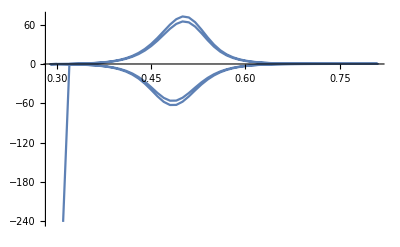

```mathematica
ListLinePlot[Cases[Import["test.txt","Table"],{_Real,_Real}],PlotRange->All]
```

```mathematica
length_,dimension_,density_,reduceddensity_,standardVolt_,n_,T_,d1_,dreduced_,electrodeposition_,ElectrodePositionOxidizedD_,ElectrodePositionReducedD_,init_,start_,end_,scanrate_,segment_,Logfilename_,ResultFileName_
```

```mathematica
Table[CVSimulation203[30,2,4,2,0.5,1,300,0.001,0.001,Tuples[Table[q,{q,10,20}],2],0.0001,0.0001,0.3,0.3,0.7,0.001*i,4,"ScanRate"<>ToString[i]<>"Log.txt","ScanRate"<>ToString[i]<>".txt"],{i,1,50,7}];
Table[CVSimulation203[30,2,4*i,2*i,0.5,1,300,0.001,0.001,Tuples[Table[q,{q,10,20}],2],0.0001,0.0001,0.3,0.3,0.7,0.01,4,"Density"<>ToString[10i]<>"Log.txt","Density"<>ToString[10i]<>".txt"],{i,0.2,2,0.2}];
Table[CVSimulation203[30,2,4,2,0.5,1,300*i,0.001*i^(3/2),0.001*i^(3/2),Tuples[Table[q,{q,10,20}],2],0.0001*i^(3/2),0.0001*i^(3/2),0.3,0.3,0.7,0.01,4,"Temperature"<>ToString[10i]<>"Log.txt","Temperature"<>ToString[10i]<>".txt"],{i,0.5,2,0.1}];
Table[CVSimulation203[30,2,4,2,0.5,1,300*i,0.001*i^(3/2),0.001*i^(3/2),Tuples[Table[q,{q,15+i,15-i}],2],0.0001*i^(3/2),0.0001*i^(3/2),0.3,0.3,0.7,0.01,4,"ElectrodeBox"<>ToString[i]<>"Log.txt","ElectodeBox"<>ToString[i]<>".txt"],{i,0,10}];
```

```mathematica
Tuples[Table[q,{q,15+0,15-0}],2]
```

{{15,15}}